# Quad Prog min 0.5 x.G.x+c.x A_e.x=b_e and A_i.x≥b_i

## 16.6 Interior Point method Implementation Algorithm 16.4 p484/506 min 0.5 x.G.x+c.x A.x≥b

Initialize with feasible point (x_0,y_0,λ_0) i.e. y_0=A.x_0-b≥0_n and λ_0≥0_n

Iterate “to convergence” k=0,1,2,3,…

(x,y,λ)=(x_k,y_k,λ_k) and solve (16.58) with σ=0 to get (Δx^aff,Δy^aff,Δλ^aff).

Calculate μ=(y.λ)/m

Calculate (α̂)_aff=Max[0≤a≤1: (y,λ)+α(Δy^aff,Δλ^aff)≥0]

Calculate μ_aff=((y +  (α̂)_aff Δy^aff).(λ + (α̂)_aff Δλ^aff))/m

Set σ=(μ_aff/μ)^3

Solve 16.67 for (Δx,Δy,Δλ)

Choose τ_k∈(0,1) and set α̂=min(α_τ_k^pri,α_τ_k^dual) (see 16.66)

Update (x_k,y_k,λ_k)=(x_k,y_k,λ_k)+α̂(Δx,Δy,Δλ)

There is quite a lot of stuff to be defined and explained here! First
	(16.58) (G | 0 | -Aᵀ
A | -I | 0
0 | Λ | Y).(Δx
Δy
Δλ)=(-r_d
-r_p
-Λ.Y.e+σ μ e)=(-(G.x-Aᵀ.λ+c)
-(A.x-y-b))
-Λ.Y.e+σ μ e)
is just the Newton step.  Step 2.2 just estimates how far from “complementarity” the original point is. Step 2.3 works out how far you can go in the affine “Newton” direction and maintain feasibility.  Step 2.4 checks how far from “complementarity” the new trial point is.  Step 2.5 computes a new value for σ from the two complementarity gaps. Step 2.6 uses that σ in the Newton Step with the affine Λ and Y
	(16.67) (G | 0 | -Aᵀ
A | -I | 0
0 | Λ | Y).(Δx
Δy
Δλ)=(-r_d
-r_p
-(Λ.Y+ΔΛ^aff ΔY^aff)e+σ μ e)=(-(G.x-Aᵀ.λ+c)
-(A.x-y-b))
-(Λ.Y+ΔΛ^aff ΔY^aff)e+σ μ e)
Step 2.7 chooses maximum primal and dual steps sizes with the same safety factor τ
	(16.66) 	 α_τ^pri | = | Max[0≤α≤1:y+α Δy≥(1-τ)y]
α_τ^dual | = | Max[0≤α≤1:λ+α Δλ≥(1-τ)λ]
The Min ensures that both the updated slack variables y and updated Lagrange multipliers λ satisfy the feasibility conditions y+α̂ Δy≥0 and λ+α̂ Δλ≥0.  All of this manipulation is motivated by experience in the linear programming case and is designed to ensure that the “Newton” steps maintain feasibility.

Here are my code building blocks

```mathematica
NewtonMatrix[G_,A_,λ_,y_]:= Module[{m=Length[G],n=Length[λ]},
ArrayFlatten[({{G, 0, -Aᵀ}, {A, -IdentityMatrix[n], 0}, {0, DiagonalMatrix[λ], DiagonalMatrix[y]}})]
]
RHS58[G_,x_,A_,λ_,c_,y_,b_,σ_,μ_]:=Join[ {-(G.x-Aᵀ.λ+c),-(A.x-y-b),-λ*y+σ μ}]
RHS67[{G_,x_,A_,λ_,c_,y_,b_,σ_,μ_},{ΔλAff_,ΔyAff_}]:=RHS58[G,x,A,λ+ΔλAff,c,y+ΔyAff,b,σ,μ]
```

To compute the maximum feasible step

```mathematica
αStepComp[y_,Δy_]:=Module[{αs=-y/Δy},
αs=Select[αs, #>0&];
Min[1,Min[αs]]
]
```

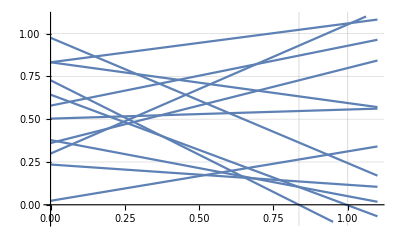

```mathematica
n=12;
y=RandomReal[{0,1},n];
Δy=RandomReal[{-1,1},n];
α=αStepComp[y,Δy];
Plot[ y+ s Δy, {s,0,1.1},
PlotRange->{-0.1,1.1},
GridLines->{{1,α}, Automatic}]
```

```mathematica
NNewtonStep[G_,A_,λ_,y_] rhs_
```